```mathematica
(*<d^†d> in the presence of a magnetic field)
```

```mathematica
(*Self-energy: Σ(ω)=(J_⊥/2π)^2 σ(ω).*)
σ[ω_]:=Exp[ω]Gamma[0,ω+10^-10 I]-Exp[-ω]Gamma[0,-ω-10^-10 I]
```

```mathematica
xarray=Table[i,{i,1,6}];
carray={1/75};
barray=Table[i,{i,0,1,0.01}];
```

```mathematica
cor[c_,b_]:=I/(2 Pi)NIntegrate[1/((ω-b)-c σ[ω]/Pi)-1/((ω-b)-c Conjugate[σ[ω]]/Pi),{ω,-20,0},Method->"GlobalAdaptive",MaxRecursion->10]
```

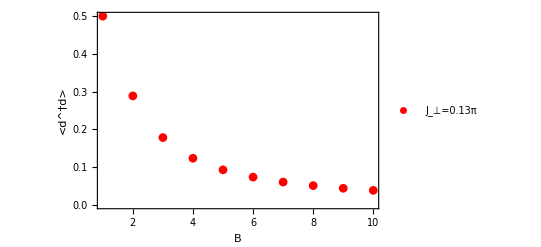

```mathematica
corarray=Table[Re[cor[carray[[m]],barray[[o]]]],{m,1,1},{o,1,10}];
ListPlot[corarray,PlotRange->All,PlotMarkers->{Automatic}, PlotStyle->Red,BaseStyle->{FontSize->14,FontFamily->"Helvetica"},Frame->True,Axes->False,FrameLabel->{"B","<d^†d>"},PlotLegends->Placed[{"J_⊥=0.13π"},{Top,Right}]]
```

```mathematica
(*Lets see what this says about our the expextation value of <Subscript[S, z]>.)
```

```mathematica
zexpectation[c_,b_]:=I/(2 Pi)NIntegrate[(1/((ω-b)-c σ[ω]/Pi)-1/((ω-b)-c Conjugate[σ[ω]]/Pi)),{ω,-20,0},Method->"GlobalAdaptive",MaxRecursion->10]-0.5
```

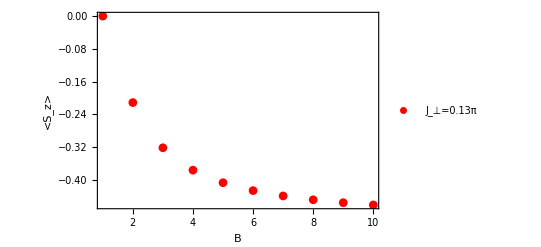

```mathematica
corarray2=Table[Re[zexpectation[carray[[m]],barray[[o]]]],{m,1,1},{o,1,10}];
ListPlot[corarray2,PlotRange->All,PlotMarkers->{Automatic}, PlotStyle->Red,BaseStyle->{FontSize->14,FontFamily->"Helvetica"},Frame->True,Axes->False,FrameLabel->{"B","<S_z>"},PlotLegends->Placed[{"J_⊥=0.13π"},{Top,Right}]]
```

```mathematica
(*When there is no field, the groundstate is a singlet, and has an equal probability to be found in a spin up or a spin down state. However, as the field is turned up, the wave function evolves and one orientation is more favorable that the other. This leads to a spin expectation value that is coupled to the magnetic field strength. In the resonant level model, the local d-level has has an ocupation probability of 0.5, when the field is switched on, it either drives itself to an occupation of 0 or 1, depending on the direction of the field.)
```

```mathematica
(*Define the modified step function*)
st[ω_,x_]:=Exp[ω](UnitStep[-x]+I Gamma[0,-ω(I x-1)]/(2Pi))-Exp[-ω]I Gamma[0,-ω(I x +1)]/(2Pi)
```

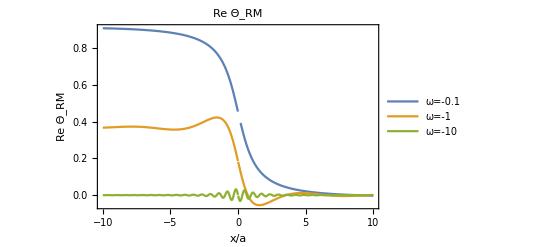

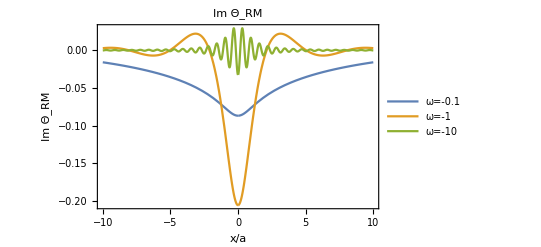

```mathematica
(*Examine regularized step function for several ω*)
p1a=Plot[{Re[st[-10^-1,x]],Re[st[-10^0,x]],Re[st[-10^1,x]]},{x,-10,10},BaseStyle->{FontSize->14,FontFamily->"Helvetica"},PlotLabel->"Re Θ_RM",Frame->True,Axes->False,FrameLabel->{"x/a","Re Θ_RM"},PlotLegends->Placed[{"ω=-0.1","ω=-1","ω=-10"},{Left,Top}]]
p1b=Plot[{Im[st[-10^-1,x]],Im[st[-10^0,x]],Im[st[-10^1,x]]},{x,-10,10},BaseStyle->{FontSize->14,FontFamily->"Helvetica"},PlotLabel->"Im Θ_RM",Frame->True,Axes->False,FrameLabel->{"x/a","Im Θ_RM"},PlotLegends->Placed[{"ω=-0.1","ω=-1","ω=-10"},{Left,Bottom}],PlotRange->All]
```

```mathematica
(*This multiplied by the original regularized step function Subscript[θ, R](x))
```

```mathematica
both[ω_,x_]:=Exp[ω](UnitStep[x]+I Gamma[0,ω(I x+1)]/(2Pi))-Exp[-ω]I Gamma[0,ω(I x -1)]/(2Pi) Exp[ω](UnitStep[-x]+I Gamma[0,-ω(I x-1)]/(2Pi))-Exp[-ω]I Gamma[0,-ω(I x +1)]/(2Pi)
```

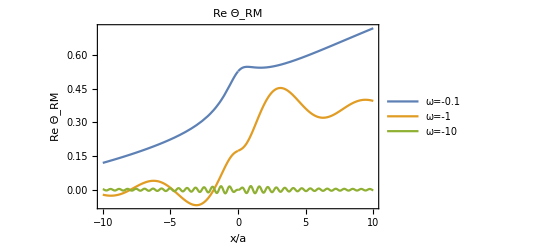

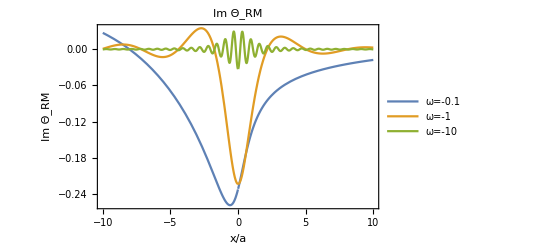

```mathematica
(*Examine regularized step function for several ω*)
p1a=Plot[{Re[both[-10^-1,x]],Re[both[-10^0,x]],Re[both[-10^1,x]]},{x,-10,10},BaseStyle->{FontSize->14,FontFamily->"Helvetica"},PlotLabel->"Re Θ_RM",Frame->True,Axes->False,FrameLabel->{"x/a","Re Θ_RM"},PlotLegends->Placed[{"ω=-0.1","ω=-1","ω=-10"},{Left,Top}]]
p1b=Plot[{Im[both[-10^-1,x]],Im[both[-10^0,x]],Im[both[-10^1,x]]},{x,-10,10},BaseStyle->{FontSize->14,FontFamily->"Helvetica"},PlotLabel->"Im Θ_RM",Frame->True,Axes->False,FrameLabel->{"x/a","Im Θ_RM"},PlotLegends->Placed[{"ω=-0.1","ω=-1","ω=-10"},{Left,Bottom}],PlotRange->All]
```